```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Read the data file and reshape it *)
```

```mathematica
ncol=6;c=1.619436525;
data=ReadList["/home/romaingrvl/MEGAsync/thèse/freefem/spinning_mini_BS/data/mathematica/bs_mat_om=0.9_m=0_c=1.619436525.out",Number];
data=data/.$Failed->0;
nline=Length[data]/ncol;
datashaped=ArrayReshape[data,{nline,ncol}]
```

```mathematica
(* Check the values of the grid bounds *)
```

```mathematica
xmin=Min[datashaped[[All,1]]]
xmax=Max[datashaped[[All,1]]]
θmin=Min[datashaped[[All,2]]]
θmax=Max[datashaped[[All,2]]]
```

0

1

0

1.5708

```mathematica
(* Useful things for later *)
```

```mathematica
(*gridx=DeleteDuplicates[datashaped[[All,1]]];
R[x_]:=c x/(1-x);*)
```

```mathematica
(* Construct tabulated values of the energy density in compactified coordinates and interpolate *)
```

```mathematica
dataTtt=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,5]]},{i,nline}];
```

```mathematica
(* ϕ: scalar field profile in compactified coordinates 
ϕρz: scalar field profile in cylindrical coordinates *)
```

```mathematica
Ttt=Interpolation[dataTtt,InterpolationOrder->3]
Tttρz[ρ_,z_]:=Ttt[Sqrt[ρ^2+z^2]/(Sqrt[ρ^2+z^2]+c),ArcTan[Abs[z],ρ]]
Tttxyz[x_,y_,z_]:=Tttρz[Sqrt[x^2+y^2],z]
```

InterpolatingFunction[…]

```mathematica
Plot3D[Ttt[x,θ],{x,xmin,xmax},{θ,θmin,θmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
ρmax=10;zmax=15;
Plot3D[Tttρz[ρ,z],{ρ,0,ρmax},{z,-zmax,zmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
(* 3D plot of isosurfaces *)
```

{0.009,0.0035,0.0012}

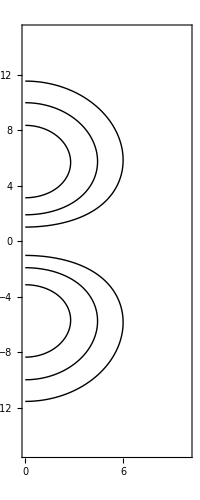

```mathematica
val={0.009,0.0035,0.0012}
ContourPlot[Tttρz[ρ,z],{ρ,0,ρmax},{z,-zmax,zmax},Contours->val,ContourShading->False,AspectRatio->Automatic,PlotPoints->100]
```

```mathematica
ρmax3D=8;zmax3D=13;
ContourPlot3D[Tttxyz[x,y,z],{x,-ρmax3D,ρmax3D},{y,0,ρmax3D},{z,-zmax3D,zmax3D},Contours->val,ContourStyle->Directive[LightBlue,Specularity[White,300]],Boxed->False,Mesh->None,BoxRatios->Automatic,Axes->False]
```

-Graphics3D-